```mathematica
SetPlotDefaults["Talk"]
```

```mathematica
<<Presentations`
```

```mathematica
?Presentations
```

Information::notfound: Symbol "Presentations" not found.

```mathematica
PresentationsHelp
```

PresentationsHelp

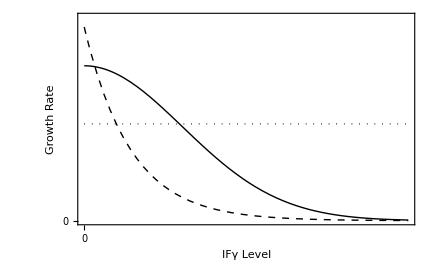

```mathematica
x[0]=0.8;
x[1] = -0;
x[2]=3;

y[0]=1;
y[1] = 1;
z[0] = 0.5;

func[1][t_]:= x[0] Exp[-(t - x[1])^2/x[2]^2];
func[2][t_]:=y[0] Exp[- t y[1]];
func[3][t_]:=z[0];
tmax = 7;
Plot[Evaluate[Table[func[i][t], {i, 3}]], {t, 0, tmax},
FrameTicks->{{0}, {0}},
PlotStyle->{Black, {Black, Dashed}, {Black, Dotted}},
PlotRange->{{0, tmax}, {0, 1.05}},
Frame->{True, True, False, False},
FrameLabel->{"IFγ Level", "Growth Rate"}
]

Plot[Evaluate[Table[func[i][t], {i, 3}]], {t, 0, tmax},
FrameTicks->{{0}, {0}},
PlotStyle->{Black, {Black, Dashed}, {Black, Dotted}},
PlotRange->{{0, tmax}, {0, 1.05}},
Frame->{True, True, False, False},
FrameLabel->{"IFγ Level", "Growth Rate"}
]
```